# Polyhedra with textured faces

### Polyhedra with a different national flag on each face

```mathematica
$polyhedrons={"Tetrahedron","RhombicHexecontahedron","Hexecontahedron"}~Join~PolyhedronData["Platonic"]
$polyhedron=$polyhedrons[[5]]
```

{Tetrahedron,RhombicHexecontahedron,Hexecontahedron,Cube,Dodecahedron,Icosahedron,Octahedron,Tetrahedron}

Dodecahedron

```mathematica
PolyhedronData[$polyhedron,"Image"]
```

-Graphics3D-

```mathematica
PolyhedronData[$polyhedron,"Faces"]
```

GraphicsComplex[{{-√(1+2/(√5)),0,Root[1-20 #1^2+80 #1^4&,3]},{√(1+2/(√5)),0,Root[1-20 #1^2+80 #1^4&,2]},{Root[1-20 #1^2+80 #1^4&,1],1/4 (-3-√5),Root[1-20 #1^2+80 #1^4&,3]},{Root[1-20 #1^2+80 #1^4&,1],1/4 (3+√5),Root[1-20 #1^2+80 #1^4&,3]},{√(5/8+11/(8 √5)),1/4 (-1-√5),Root[1-20 #1^2+80 #1^4&,3]},{√(5/8+11/(8 √5)),1/4 (1+√5),Root[1-20 #1^2+80 #1^4&,3]},{Root[1-20 #1^2+80 #1^4&,2],1/4 (-1-√5),√(5/8+11/(8 √5))},{Root[1-20 #1^2+80 #1^4&,2],1/4 (1+√5),√(5/8+11/(8 √5))},{-1/2 √(1+2/(√5)),-1/2,Root[1-100 #1^2+80 #1^4&,1]},{-1/2 √(1+2/(√5)),1/2,Root[1-100 #1^2+80 #1^4&,1]},{√(1/4+1/(2 √5)),-1/2,√(5/8+11/(8 √5))},{√(1/4+1/(2 √5)),1/2,√(5/8+11/(8 √5))},{√(1/10 (5+√5)),0,Root[1-100 #1^2+80 #1^4&,1]},{Root[1-100 #1^2+80 #1^4&,1],1/4 (-1-√5),Root[1-20 #1^2+80 #1^4&,2]},{Root[1-100 #1^2+80 #1^4&,1],1/4 (1+√5),Root[1-20 #1^2+80 #1^4&,2]},{Root[1-5 #1^2+5 #1^4&,1],0,√(5/8+11/(8 √5))},{Root[1-20 #1^2+80 #1^4&,3],1/4 (-1-√5),Root[1-100 #1^2+80 #1^4&,1]},{Root[1-20 #1^2+80 #1^4&,3],1/4 (1+√5),Root[1-100 #1^2+80 #1^4&,1]},{√(1/8+1/(8 √5)),1/4 (-3-√5),Root[1-20 #1^2+80 #1^4&,2]},{√(1/8+1/(8 √5)),1/4 (3+√5),Root[1-20 #1^2+80 #1^4&,2]}},Polygon[{{15,10,9,14,1},{2,6,12,11,5},{5,11,7,3,19},{11,12,8,16,7},{12,6,20,4,8},{6,2,13,18,20},{2,5,19,17,13},{4,20,18,10,15},{18,13,17,9,10},{17,19,3,14,9},{3,7,16,1,14},{16,8,4,15,1}}]]

```mathematica
vertices=With[{v=PolyhedronData[$polyhedron,"Faces"][[1]]},MapThread[Rule,{Range[Length[v]],v}]]
faceIndices=PolyhedronData[$polyhedron,"Faces"][[2]]
```

{1→{-√(1+2/(√5)),0,Root[1-20 #1^2+80 #1^4&,3]},2→{√(1+2/(√5)),0,Root[1-20 #1^2+80 #1^4&,2]},3→{Root[1-20 #1^2+80 #1^4&,1],1/4 (-3-√5),Root[1-20 #1^2+80 #1^4&,3]},4→{Root[1-20 #1^2+80 #1^4&,1],1/4 (3+√5),Root[1-20 #1^2+80 #1^4&,3]},5→{√(5/8+11/(8 √5)),1/4 (-1-√5),Root[1-20 #1^2+80 #1^4&,3]},6→{√(5/8+11/(8 √5)),1/4 (1+√5),Root[1-20 #1^2+80 #1^4&,3]},7→{Root[1-20 #1^2+80 #1^4&,2],1/4 (-1-√5),√(5/8+11/(8 √5))},8→{Root[1-20 #1^2+80 #1^4&,2],1/4 (1+√5),√(5/8+11/(8 √5))},9→{-1/2 √(1+2/(√5)),-1/2,Root[1-100 #1^2+80 #1^4&,1]},10→{-1/2 √(1+2/(√5)),1/2,Root[1-100 #1^2+80 #1^4&,1]},11→{√(1/4+1/(2 √5)),-1/2,√(5/8+11/(8 √5))},12→{√(1/4+1/(2 √5)),1/2,√(5/8+11/(8 √5))},13→{√(1/10 (5+√5)),0,Root[1-100 #1^2+80 #1^4&,1]},14→{Root[1-100 #1^2+80 #1^4&,1],1/4 (-1-√5),Root[1-20 #1^2+80 #1^4&,2]},15→{Root[1-100 #1^2+80 #1^4&,1],1/4 (1+√5),Root[1-20 #1^2+80 #1^4&,2]},16→{Root[1-5 #1^2+5 #1^4&,1],0,√(5/8+11/(8 √5))},17→{Root[1-20 #1^2+80 #1^4&,3],1/4 (-1-√5),Root[1-100 #1^2+80 #1^4&,1]},18→{Root[1-20 #1^2+80 #1^4&,3],1/4 (1+√5),Root[1-100 #1^2+80 #1^4&,1]},19→{√(1/8+1/(8 √5)),1/4 (-3-√5),Root[1-20 #1^2+80 #1^4&,2]},20→{√(1/8+1/(8 √5)),1/4 (3+√5),Root[1-20 #1^2+80 #1^4&,2]}}

Polygon[{{15,10,9,14,1},{2,6,12,11,5},{5,11,7,3,19},{11,12,8,16,7},{12,6,20,4,8},{6,2,13,18,20},{2,5,19,17,13},{4,20,18,10,15},{18,13,17,9,10},{17,19,3,14,9},{3,7,16,1,14},{16,8,4,15,1}}]

```mathematica
ClearAll[getRandomFlag,$usedCountries]
$usedCountries={};
getRandomFlag[]:=Module[
{flag,country},
While[
Head[country]=!=Entity||MemberQ[$usedCountries,country],
country=Quiet@RandomEntity["Country"]//Echo;
];
PrependTo[$usedCountries,country];
While[
Head[flag]=!=Graphics,
flag=CountryData[country,"Flag"]//Echo
];
flag
]
```

Swaziland

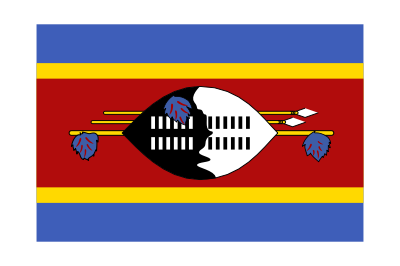

-Graphics-

```mathematica
$usedCountries={};
getRandomFlag[]
```

South Sudan

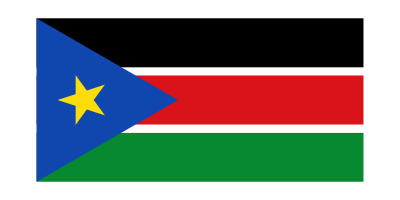

South Sudan

Iraq

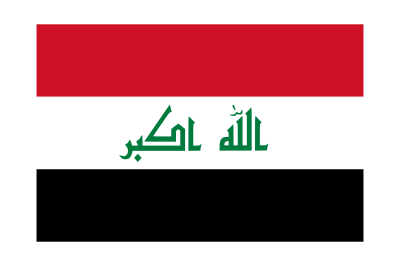

South Sudan

Swaziland

-Graphics-

{5.45532,{-Graphics-,-Graphics-,-Graphics-}}

```mathematica
$usedCountries={};
Table[getRandomFlag[],{3}]//AbsoluteTiming
```

```mathematica
getRandomTexture[]:=Texture[{getRandomFlag[],ExampleData[{"ColorTexture","WhiteMarble"}]}[[1]]]
```

French Guiana

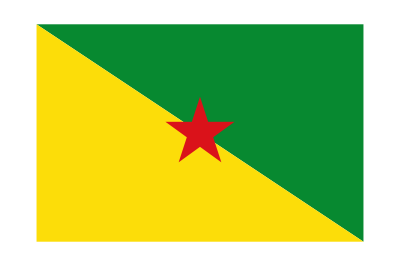

Greece

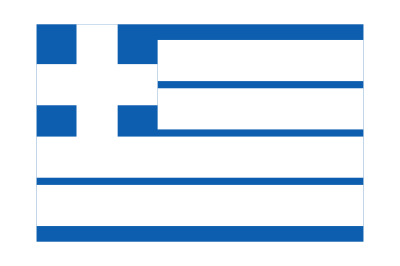

Finland

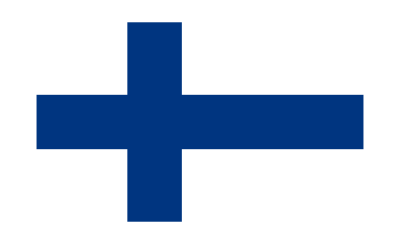

South Sudan

-Graphics-

Albania

-Graphics-

South Sudan

Fiji

-Graphics-

Belize

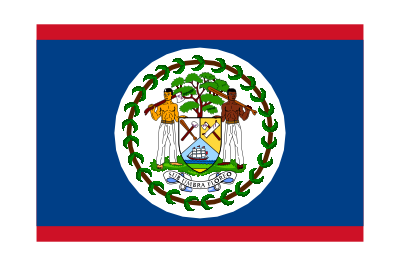

Burundi

-Graphics-

Cambodia

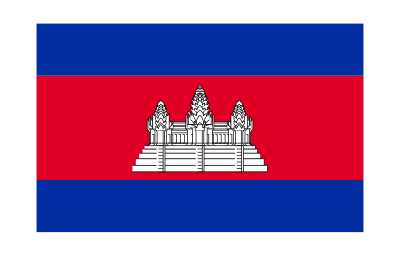

South Sudan

Bahamas

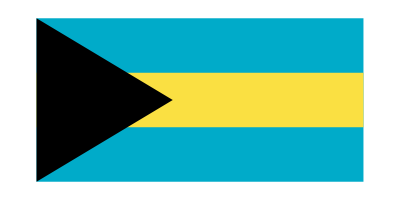

South Sudan

South Sudan

Burkina Faso

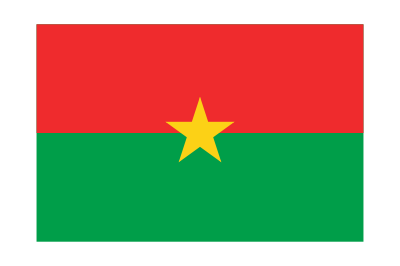

Uruguay

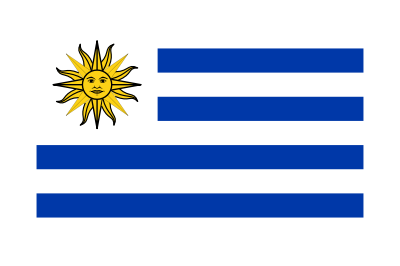

Myanmar

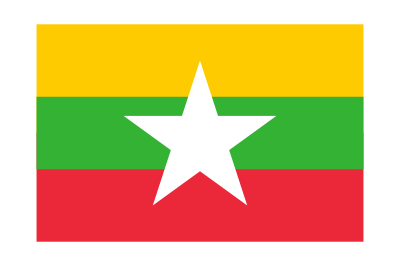

-Graphics3D-

```mathematica
$usedCountries={};
Composition[
Graphics3D[#, Boxed-> False,Lighting-> "Neutral",ImageSize-> 500]&,
(*System`Echo,*)
Prepend[#,EdgeForm[{White,Thick}]]&,
Prepend[#,getRandomTexture[]]&,
Join@@#&,
{#,getRandomTexture[]}&/@#&,
Map[Polygon[Replace[#,vertices,{1}],VertexTextureCoordinates->Replace[#,vertices,{1}]]&,#]&,
First
][faceIndices]
```

### References

```mathematica
RandomEntity["Country"]
```

South Sudan